```mathematica
Names["Global`*"]
```

```mathematica
vars = Sort[{"x864","x868"}, ToExpression[StringDrop[#1,1]]<ToExpression[StringDrop[#2,1]]&];
```

```mathematica
Table[SimpleGraph[Graph[Map[#[[1]]<->#[[2]]&,ToExpression[v]]]],{v,vars}]
```

```mathematica
e2p[edge_]:=Sort[{edge[[1]],edge[[2]]}]
e2p[23<->1]
```

{1,23}

```mathematica
NotBridgedQ[graph_]:=Length[Complement[Map[e2p,EdgeList[graph]],DeleteDuplicates[Map[e2p,Flatten[FindCycle[graph,∞,All]]]]]]==0
```

```mathematica
NotBridgedQ[CompleteGraph[4]]
```

True

```mathematica
SimpleGraphQ
```

```mathematica
PrunableQ[graph_]:=MemberQ[VertexDegree[graph],1]
PrunableQ[CompleteGraph[4]]
```

False

```mathematica
PlanarGraphQ[graph]
```

```mathematica
not02degQ[graph_]:=Block[{vd=VertexDegree[graph]},MemberQ[vd,0]||MemberQ[vd,1]||MemberQ[vd,2]]
```

```mathematica
GoodQ[graph_]:=
Block[{sq=SimpleGraphQ[graph]},Piecewise[{{Block[{prq=not02degQ[graph]},Piecewise[{{Block[{plq=PlanarGraphQ[graph]},Piecewise[{{Block[{ccq=Length[ConnectedComponents[graph]]==1},Piecewise[{{NotBridgedQ[graph], ccq}, {False, ¬ccq}}]], plq}, {False, ¬plq}}]], ¬prq}, {False, prq}}]], sq}, {False, ¬sq}}]]
```

```mathematica
Table[GoodQ[CompleteGraph[i]],{i,2,5}]
```

{False,False,True,False}

```mathematica
Length[GraphData[3;;18]]
```

4108

```mathematica
goods={};
gd=GraphData[3;;18];
gdl=Length[gd]
Timing[Monitor[Do[If[GoodQ[GraphData[gd[[i]]]],AppendTo[goods,gd[[i]]]],{i,1,gdl}],i]]
Length[goods]
```

4108

{106.10933,Null}

382

```mathematica
gcy3=Graph([(0,1),(1,2),(2,0)],directed=False)
```

```mathematica
g2py[graphname_,toname_]:=StringJoin["graph",ToString[toname]," = ","Graph([",StringDrop[StringDrop[ToString[Map[StringJoin["(",StringReplace[ToString[#],{"<->"->","}],")"]&,EdgeList[GraphData[graphname]]]],-1],1],"], directed = False)\n"]
```

```mathematica
Export["graphlist.py",StringJoin[Table[g2py[goods[[i]],i-1],{i,1,Length[goods]}]],"TEXT"]
```

graphlist.py

```mathematica
Length[goods]
```

120

```mathematica
Map[GraphData,goods]
```

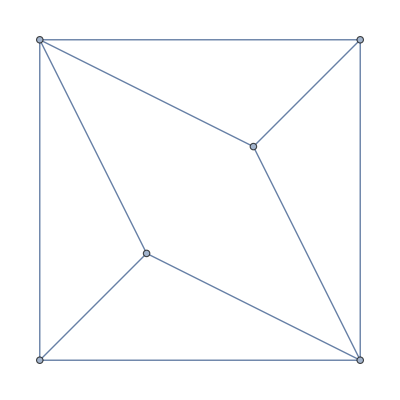

```mathematica
GraphData[goods[[1]]]
```

```mathematica
Select[GraphData[20],PlanarGraphQ[#]&&DeleteDuplicates[VertexDegree[GraphData[#]]]=={4}&]
```

{}

```mathematica
Normal[AdjacencyMatrix[CompleteGraph[5]]]//MatrixForm
```

```mathematica
pcc[n_]:=Block[{id=PadLeft[IntegerDigits[n,2],10]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],d=id[[4]],e=id[[5]],f=id[[6]],g=id[[7]],h=id[[8]],i=id[[9]],j=id[[10]]},
Length[FindCycle[AdjacencyGraph[({{0, a, b, c, d}, {1-a, 0, e, f, g}, {1-b, 1-e, 0, h, i}, {1-c, 1-f, 1-h, 0, j}, {1-d, 1-g, 1-i, 1-j, 0}})],∞,All]]]]
```

```mathematica
hcc[x_]:=Block[{id=PadLeft[IntegerDigits[x,2],15]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],d=id[[4]],e=id[[5]],f=id[[6]],g=id[[7]],h=id[[8]],i=id[[9]],j=id[[10]],k=id[[11]],l=id[[12]],m=id[[13]],n=id[[14]],o=id[[15]]},
Length[FindCycle[AdjacencyGraph[({{0, a, b, c, d, k}, {1-a, 0, e, f, g, l}, {1-b, 1-e, 0, h, i, m}, {1-c, 1-f, 1-h, 0, j, n}, {1-d, 1-g, 1-i, 1-j, 0, o}, {1-k, 1-l, 1-m, 1-n, 1-o, 0}})],∞,All]]]]
hcg[x_]:=Block[{id=PadLeft[IntegerDigits[x,2],15]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],d=id[[4]],e=id[[5]],f=id[[6]],g=id[[7]],h=id[[8]],i=id[[9]],j=id[[10]],k=id[[11]],l=id[[12]],m=id[[13]],n=id[[14]],o=id[[15]]},
AdjacencyGraph[({{0, a, b, c, d, k}, {1-a, 0, e, f, g, l}, {1-b, 1-e, 0, h, i, m}, {1-c, 1-f, 1-h, 0, j, n}, {1-d, 1-g, 1-i, 1-j, 0, o}, {1-k, 1-l, 1-m, 1-n, 1-o, 0}})]]]
```

```mathematica
pcc[n_]:=Block[{id=PadLeft[IntegerDigits[n,2],10]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],d=id[[4]],e=id[[5]],f=id[[6]],g=id[[7]],h=id[[8]],i=id[[9]],j=id[[10]]},
Length[FindCycle[AdjacencyGraph[({{0, a, b, c, d}, {1-a, 0, e, f, g}, {1-b, 1-e, 0, h, i}, {1-c, 1-f, 1-h, 0, j}, {1-d, 1-g, 1-i, 1-j, 0}})],∞,All]]]]
pcg[n_]:=Block[{id=PadLeft[IntegerDigits[n,2],10]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],d=id[[4]],e=id[[5]],f=id[[6]],g=id[[7]],h=id[[8]],i=id[[9]],j=id[[10]]},
AdjacencyGraph[({{0, a, b, c, d}, {1-a, 0, e, f, g}, {1-b, 1-e, 0, h, i}, {1-c, 1-f, 1-h, 0, j}, {1-d, 1-g, 1-i, 1-j, 0}})]]]
```

```mathematica
tcc[n_]:=Block[{id=PadLeft[IntegerDigits[n,2],6]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],e=id[[4]],f=id[[5]],h=id[[6]]},
Length[FindCycle[AdjacencyGraph[({{0, a, b, c}, {1-a, 0, e, f}, {1-b, 1-e, 0, h}, {1-c, 1-f, 1-h, 0}})],∞,All]]]]
tcg[n_]:=Block[{id=PadLeft[IntegerDigits[n,2],6]},
Block[{a=id[[1]],b=id[[2]],c=id[[3]],e=id[[4]],f=id[[5]],h=id[[6]]},
AdjacencyGraph[({{0, a, b, c}, {1-a, 0, e, f}, {1-b, 1-e, 0, h}, {1-c, 1-f, 1-h, 0}})]]]
```

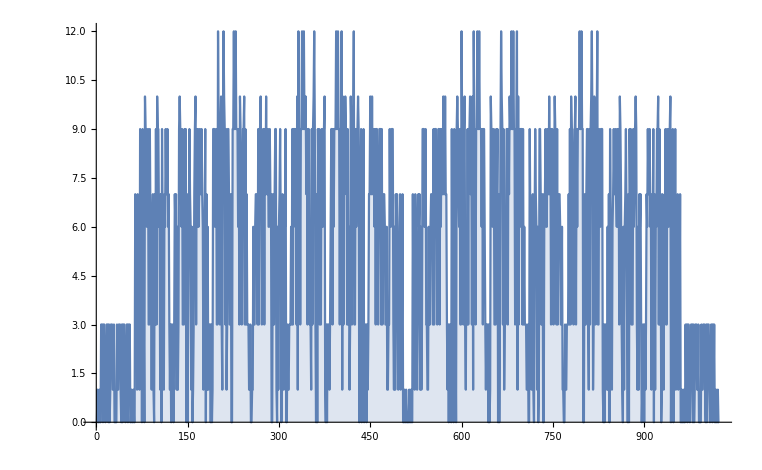

```mathematica
DiscretePlot[pcc[n],{n,0,1023},PlotRange->All]
```

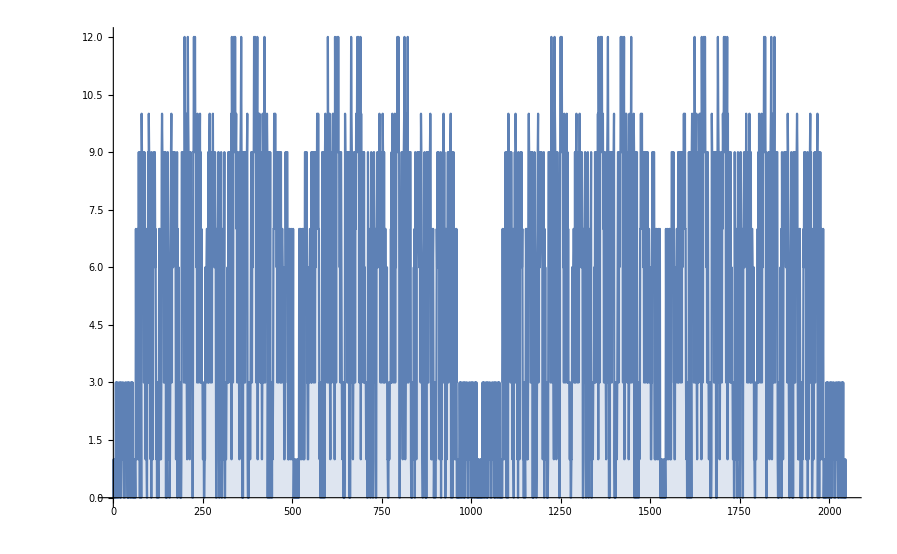

```mathematica
DiscretePlot[pcc[n],{n,1,2048},PlotRange->All]
```

```mathematica
Length[{88,184,276,344,402,440,564,600,625,696,786,817,849,881,914,946,1112,1208,1234,1265,1300,1364,1428,1457,1489,1521,1588,1618,1652,1716,1746,1778}]
```

32

```mathematica
TuttePolynomial[CompleteGraph[6],{x,y}]
```

```mathematica
Select[Flatten[Table[{x,y,24 x+50 x^2+35 x^3+10 x^4+x^5+24 y+106 x y+90 x^2 y+20 x^3 y+80 y^2+145 x y^2+45 x^2 y^2+120 y^3+105 x y^3+15 x^2 y^3+120 y^4+60 x y^4+96 y^5+24 x y^5+64 y^6+6 x y^6+35 y^7+15 y^8+5 y^9+y^10},{x,-10,10},{y,-10,10}],1],#[[3]]==32&]
```

{{-3,1,32}}

```mathematica
TuttePolynomial[CompleteGraph[5],{x,y}]
```

```mathematica
Select[Flatten[Table[{x,y,6 x+11 x^2+6 x^3+x^4+6 y+20 x y+10 x^2 y+15 y^2+15 x y^2+15 y^3+5 x y^3+10 y^4+4 y^5+y^6},{x,-4,2},{y,-2,1}],1],#[[3]]==24&]
```

{{-4,0,24},{-1,-2,24},{0,-2,24},{1,0,24},{2,-2,24}}

```mathematica
Length[{200,209,226,229,332,338,341,358,394,397,403,423,600,620,626,629,665,682,685,691,794,797,814,823}]
```

24

```mathematica
TuttePolynomial[CompleteGraph[4],{x,y}]
```

```mathematica
Select[Flatten[Table[{x,y,2 x+3 x^2+x^3+2 y+4 x y+3 y^2+y^3},{x,-10,10},{y,-10,10}],1],#[[3]]==24&]
```

{{-3,-3,24},{0,2,24},{2,0,24}}

```mathematica
few0=Table[tcc[n],{n,1,64}];
Flatten[Position[few0,Max[few0]]]
Map[tcg,%]
```

```mathematica
Length[{8,10,12,13,17,18,19,21,24,25,26,29,34,37,38,39,42,44,45,46,50,51,53,55}]
```

24

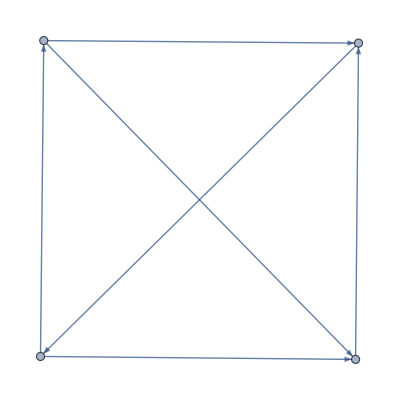
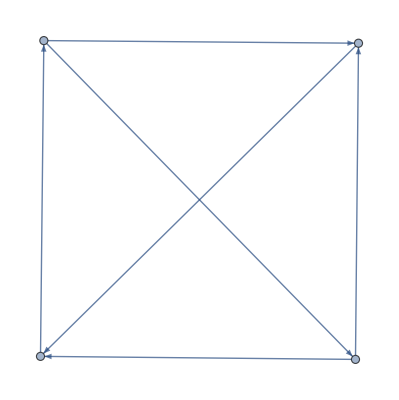
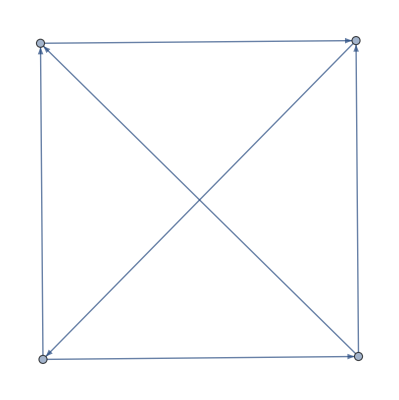
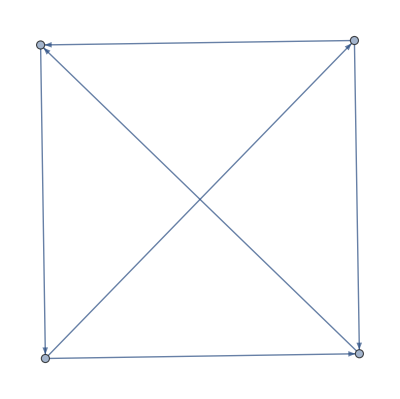
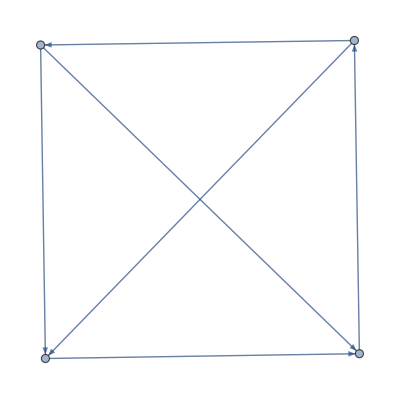
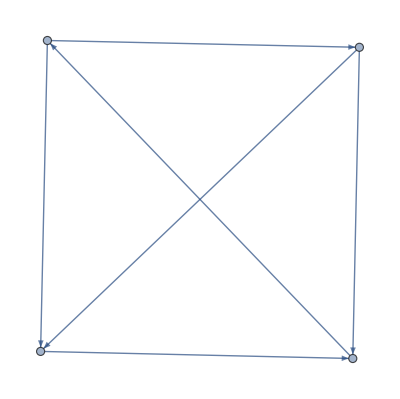
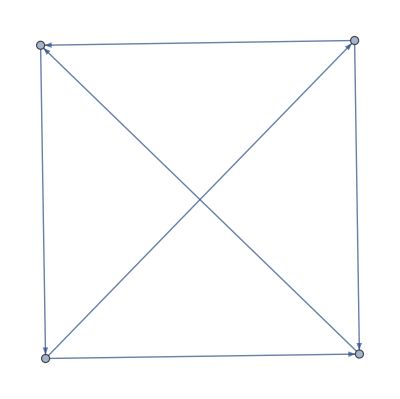
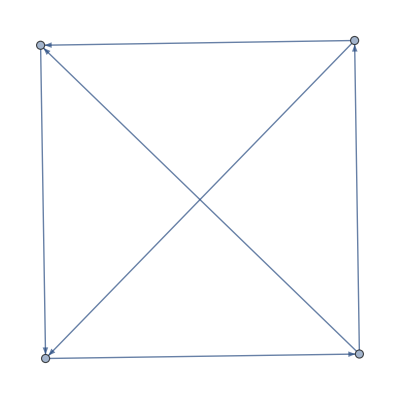
```mathematica
DeleteDuplicates[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{88,184,276,344,402,440,564,600,625,696,786,817,849,881,914,946,1112,1208,1234,1265,1300,1364,1428,1457,1489,1521,1588,1618,1652,1716,1746,1778}

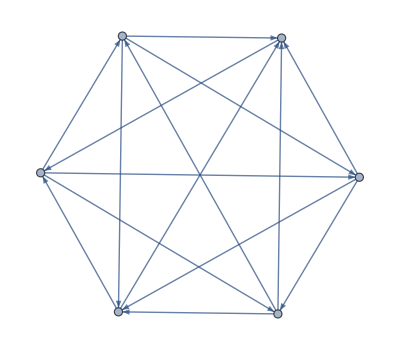
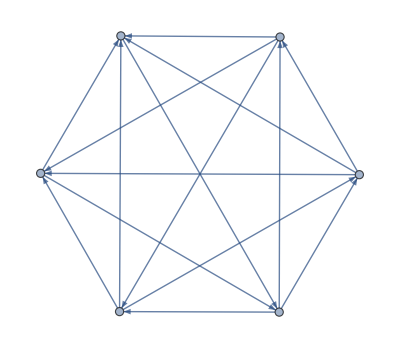
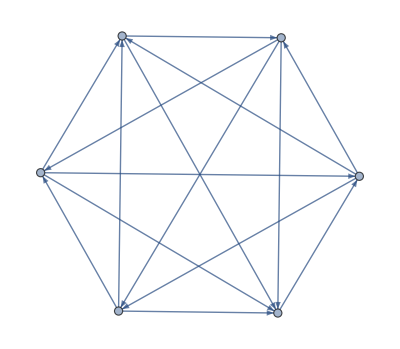
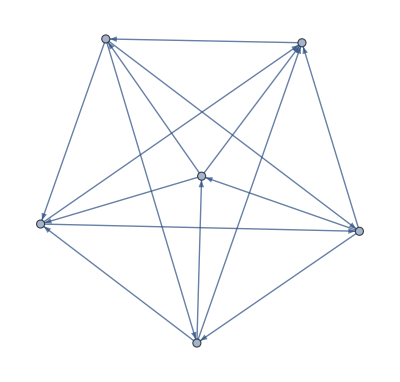
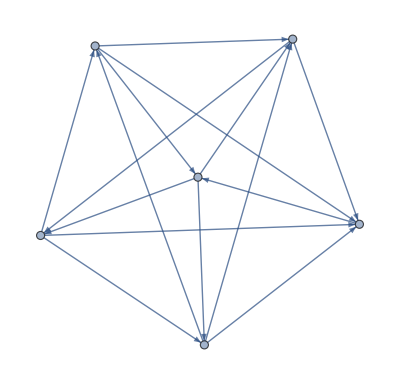
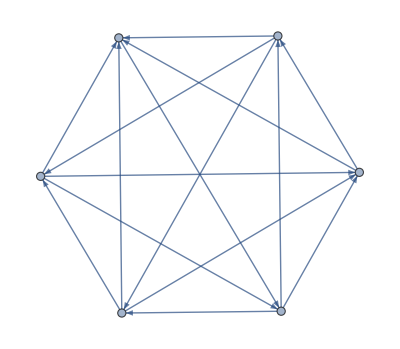
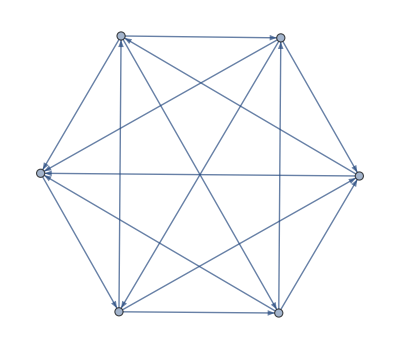
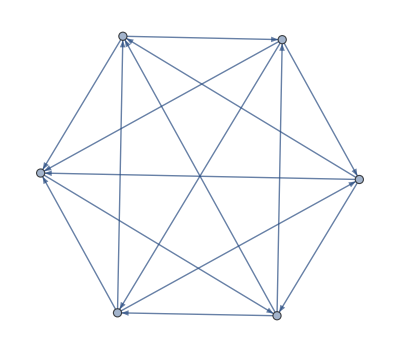

```mathematica
few2=Table[hcc[n],{n,1,2048}];
Flatten[Position[few2,Max[few2]]]
Map[hcg,%]
```

```mathematica
Map[Sort,Map[VertexInDegree,Out[413]]]
```

{{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4},{2,2,2,2,3,4}}

{200,209,226,229,332,338,341,358,394,397,403,423,600,620,626,629,665,682,685,691,794,797,814,823}

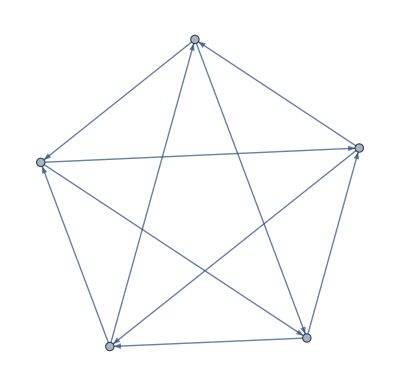
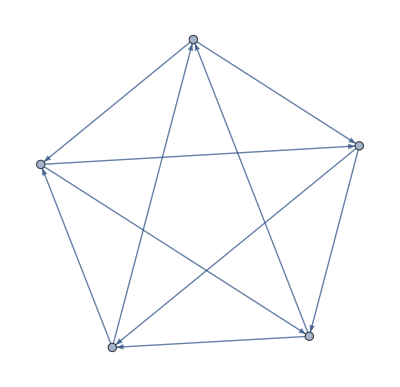
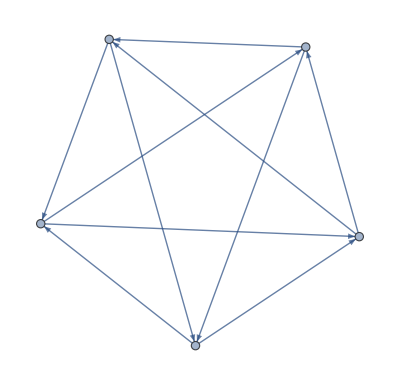
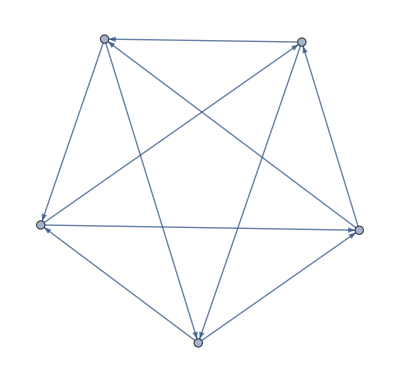
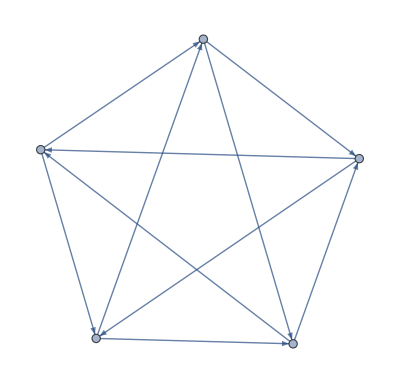
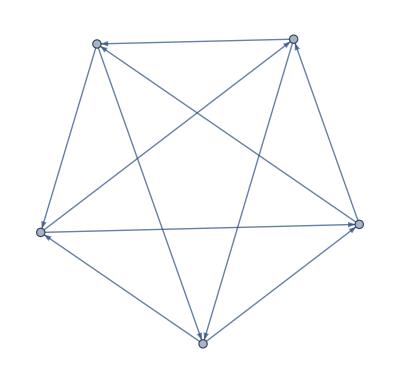
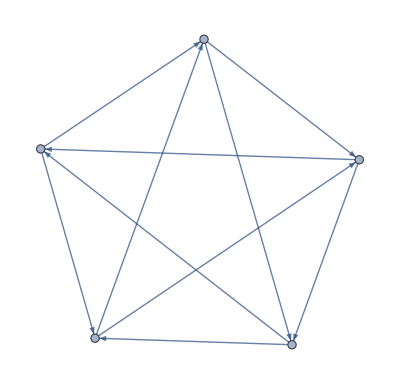
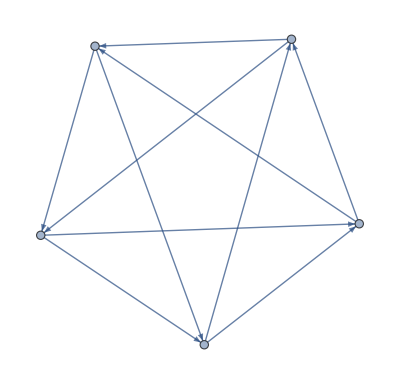

```mathematica
few=Table[pcc[n],{n,1,1024}];
Flatten[Position[few,Max[few]]]
Map[pcg,%]
```

```mathematica
Map[VertexInDegree,Out[399]]
```

{{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2},{2,2,2,2,2}}

```mathematica
FindCycle[CompleteGraph[5],∞,All]
```

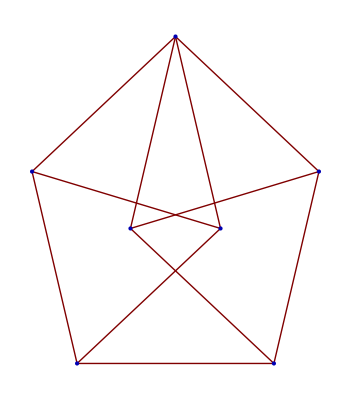
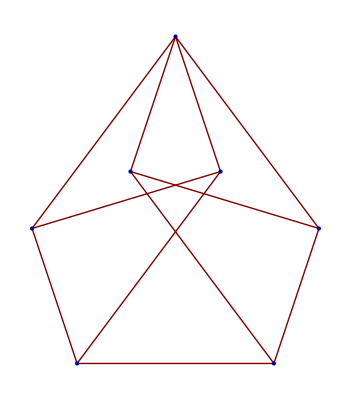
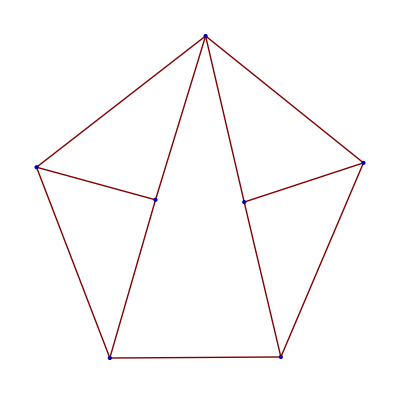

```mathematica
GraphData[goods[[325]],"AllImages"]
```

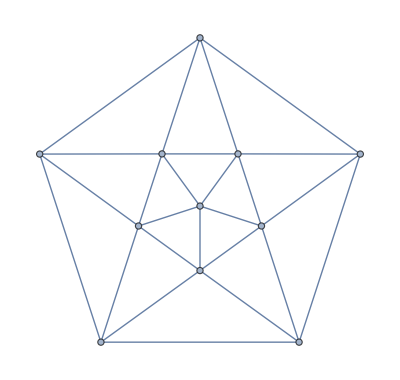
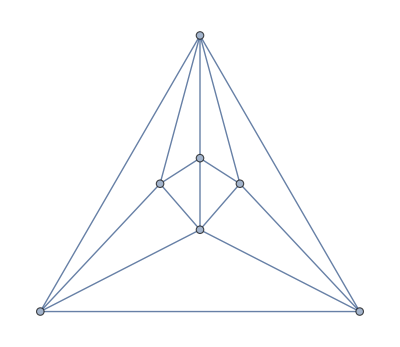
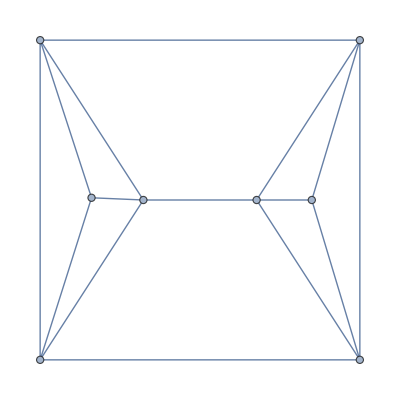
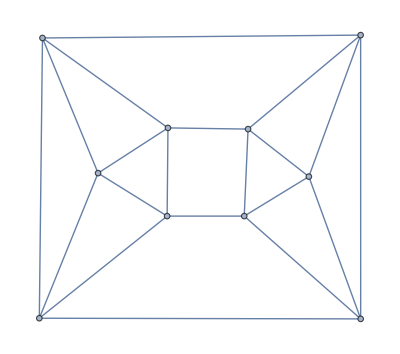
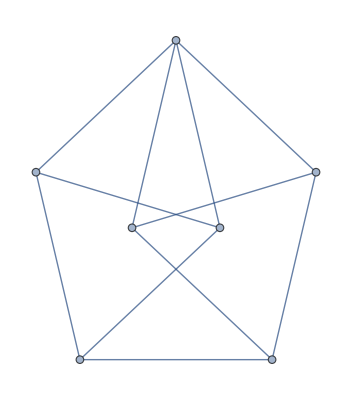
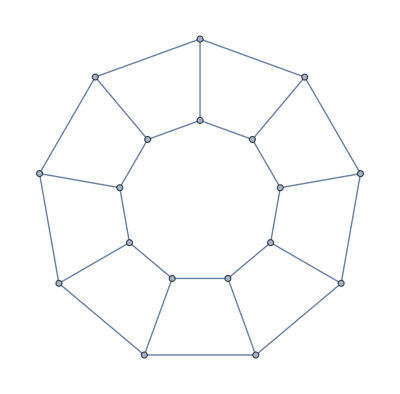
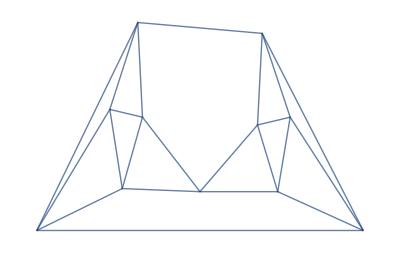
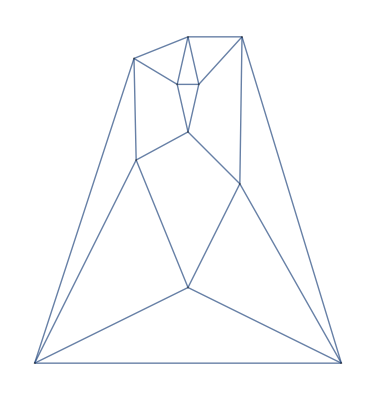

```mathematica
Table[GraphData[goods[[i]]],{i,{280,282,283,284,325,333,336,337,352,355}}]
```

```mathematica
Map[Length[EdgeList[#]]&,%]
```

{25,15,15,20,11,27,22,22,18,18}

```mathematica
ToExpression[StringReplace["lpy1=[[[0,1],[0,5],[0,6],[0,9]],[[0,1],[0,5],[0,6],[0,8],[0,9]],[[0,1],[0,5],[0,6],[0,7]],[[0,1],[0,5],[0,6],[0,7],[0,9]],[[0,1],[0,3],[0,7],[0,8]],[[0,1],[0,3],[0,6],[0,7],[0,8]],[[0,1],[0,3],[0,5],[0,9]],[[0,1],[0,3],[0,5],[0,8]],[[0,1],[0,3],[0,4],[0,9]],[[0,1],[0,3],[0,4],[0,7]]]",{"["->"{","]"->"}"}]]
```

{{{0,1},{0,5},{0,6},{0,9}},{{0,1},{0,5},{0,6},{0,8},{0,9}},{{0,1},{0,5},{0,6},{0,7}},{{0,1},{0,5},{0,6},{0,7},{0,9}},{{0,1},{0,3},{0,7},{0,8}},{{0,1},{0,3},{0,6},{0,7},{0,8}},{{0,1},{0,3},{0,5},{0,9}},{{0,1},{0,3},{0,5},{0,8}},{{0,1},{0,3},{0,4},{0,9}},{{0,1},{0,3},{0,4},{0,7}}}

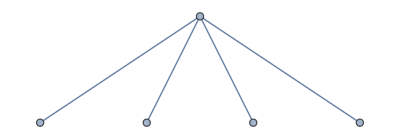

```mathematica
Graph[Map[#[[1]]<->#[[2]]&,lpy1[[1]]]]
```

```mathematica
NthOrientation[graph_,n0_]:=Block[{n=n0,out={},ones=Select[Position[Normal[AdjacencyMatrix[graph]],1],#[[1]]<#[[2]]&]},

For[i=1,i<=Length[ones],i++,Block[{nm2=Mod[n,2]},AppendTo[out,ones[[i]]->nm2];AppendTo[out,Reverse[ones[[i]]]->1-nm2];n=(n-nm2)/2]];Block[{len=Length[VertexList[graph]]},AdjacencyGraph[SparseArray[out,{len,len}]]]]
```

```mathematica
AdjacencyMatrix[CompleteGraph[3]]//Normal//MatrixForm
```

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)

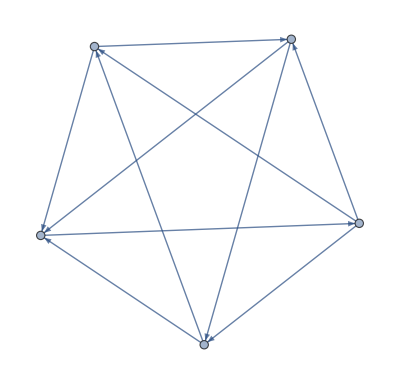

```mathematica
NthOrientation[CompleteGraph[5],235]
```

```mathematica
wellorientations[graph_]:=Block[{few=ParallelTable[Length[FindCycle[NthOrientation[graph,n],∞,All]],{n,1,2^Length[EdgeList[graph]]}]},
Map[NthOrientation[graph,#]&,Flatten[Position[few,Max[few]]]]]
```

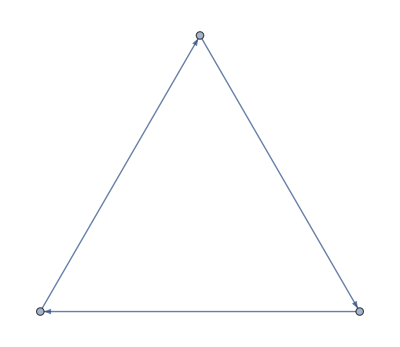

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Monitor[Table[wellorientations[CompleteGraph[m]],{m,3,7}],m]
```

```mathematica
Map[Length[DeleteDuplicates[#]]&,Map[Normal[AdjacencyMatrix[#]]&,Out[109],{2}]]
```

{2,24,24,1680,240}

```mathematica
Monitor[Table[Length[wellorientations[CompleteGraph[m]]],{m,3,10}],{m,i}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1564, 9].

KernelObject::rdead: Subkernel connected through KernelObject[4, "local"] appears dead.

LaunchKernels::clone: Kernel KernelObject[4, "local", "<defunct>"] resurrected as KernelObject[5, "local"].

$Aborted

```mathematica
Timing[Length[DeleteDuplicates[Map[Normal[AdjacencyMatrix[#]]&,wellorientations[CompleteGraph[3]]]]]]
```

{0.2749,4}

```mathematica
TuttePolynomial[CompleteGraph[3],{x,y}]
Select[Flatten[Table[{x,y,%},{x,-20,20},{y,-20,20}],1],#[[3]]==4&]
```

x+x^2+y

{{-5,-16,4},{-4,-8,4},{-3,-2,4},{-2,2,4},{-1,4,4},{0,4,4},{1,2,4},{2,-2,4},{3,-8,4},{4,-16,4}}

```mathematica
Timing[Length[DeleteDuplicates[Map[Normal[AdjacencyMatrix[#]]&,wellorientations[CompleteGraph[4]]]]]]
```

{0.01853,6}

```mathematica
TuttePolynomial[CompleteGraph[4],{x,y}]
Monitor[Select[Flatten[Table[{x,y,%},{x,-20,20},{y,-20,20}],1],#[[3]]==6&],{N[x],N[y]}]
```

2 x+3 x^2+x^3+2 y+4 x y+3 y^2+y^3

{{-3,-1,6},{-1,-3,6},{0,1,6},{1,0,6}}

```mathematica
Timing[Length[DeleteDuplicates[Map[Normal[AdjacencyMatrix[#]]&,wellorientations[CompleteGraph[5]]]]]]
```

{0.05324,12}

```mathematica
TuttePolynomial[CompleteGraph[5],{x,y}]
Select[Flatten[Table[{x,y,%},{x,-20,20},{y,-20,20}],1],#[[3]]==12&]
```

6 x+11 x^2+6 x^3+x^4+6 y+20 x y+10 x^2 y+15 y^2+15 x y^2+15 y^3+5 x y^3+10 y^4+4 y^5+y^6

{}

```mathematica
Timing[Length[DeleteDuplicates[Map[Normal[AdjacencyMatrix[#]]&,wellorientations[CompleteGraph[6]]]]]]
```

{0.6682,48}

```mathematica
TuttePolynomial[CompleteGraph[6],{x,y}]
Select[Flatten[Table[{x,y,%},{x,-100,100},{y,-100,100}],1],#[[3]]==48&]
```

24 x+50 x^2+35 x^3+10 x^4+x^5+24 y+106 x y+90 x^2 y+20 x^3 y+80 y^2+145 x y^2+45 x^2 y^2+120 y^3+105 x y^3+15 x^2 y^3+120 y^4+60 x y^4+96 y^5+24 x y^5+64 y^6+6 x y^6+35 y^7+15 y^8+5 y^9+y^10

{}

```mathematica
Timing[Length[DeleteDuplicates[Map[Normal[AdjacencyMatrix[#]]&,wellorientations[CompleteGraph[7]]]]]]
```

{96.499311,240}

```mathematica
TuttePolynomial[CompleteGraph[6],{x,y}]
Select[Flatten[Table[{x,y,%},{x,-100,100},{y,-100,100}],1],#[[3]]==Last[Out[103]]&]
```

24 x+50 x^2+35 x^3+10 x^4+x^5+24 y+106 x y+90 x^2 y+20 x^3 y+80 y^2+145 x y^2+45 x^2 y^2+120 y^3+105 x y^3+15 x^2 y^3+120 y^4+60 x y^4+96 y^5+24 x y^5+64 y^6+6 x y^6+35 y^7+15 y^8+5 y^9+y^10

{}

```mathematica
Length[EdgeList[CompleteGraph[7]]]
```

```mathematica
{4,6,12,48,240}/2
```

{2,3,6,24,120}

```mathematica
{8,12,24,96,480}/4
```

{2,3,6,24,120}

```mathematica
LaplaceTransform[1/t,t,s]
```

LaplaceTransform[1/t,t,s]

```mathematica
Monitor[Table[ChromaticPolynomial[CycleGraph[n],3],{n,1,10}],n]
```

{0,6,6,18,30,66,126,258,510,1026}

```mathematica
Table[2^n+2*(-1)^n,{n,1,10}]
```

{0,6,6,18,30,66,126,258,510,1026}

```mathematica
wellorientations[WheelGraph[4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[FindCycle[Out[12][[1]],∞,All]]
```

2

```mathematica
Monitor[Table[Length[FindCycle[First[wellorientations[WheelGraph[n]]],∞,All]],{n,4,10}],n]
```

{3,5,7,10,13,17,21}

```mathematica
Length[FindCycle[First[wellorientations[WheelGraph[11]]],∞,All]]
```

25

```mathematica
Table[WheelGraph[n],{n,4,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
InterpolatingPolynomial[{{3,2},
{4,4},
{5,6},
{6,9},
{7,12},
{8,16},
{9,20}},x]
```

```mathematica
a-b==c
```

```mathematica
DeleteDuplicates[DeleteCases[Flatten[Table[{a,b,c}*Boole[a-b==c≠0],{a,0,2},{b,0,2},{c,0,2}],2],{0,0,0}]]
```

{{1,0,1},{2,0,2},{2,1,1}}

```mathematica
DeleteDuplicates[DeleteCases[Flatten[Table[{a,b,c}*Boole[a-b==c≠0],{a,0,3},{b,0,3},{c,0,3}],2],{0,0,0}]]
```

{{1,0,1},{2,0,2},{2,1,1},{3,0,3},{3,1,2},{3,2,1}}

```mathematica
Length[%]
```

6

```mathematica
{0,1}
{1,2}
```

```mathematica
fep[n_]:=Block[{l=PadLeft[IntegerDigits[n,3],6]},
Block[{a=l[[1]]+1,b=l[[2]]+1,c=l[[3]]+1,d=l[[4]]+1,e=l[[5]]+1,f=l[[6]]+1},Boole[a-d-f==0&&e+f-c==0&&d+b-e==0&&-a-b+c==0]]]
```

```mathematica
Position[Table[fep[m],{m,1,3^6}],1]
```

{{300}}

```mathematica
Map[#+1&,PadLeft[IntegerDigits[300,3],6]]
```

{2,1,3,1,2,1}

```mathematica
Select[GraphData["Triangulated"],Length[EdgeList[GraphData[#]]]<20&]
```

{{Apollonian,2},{Heptahedral,15},{Heptahedral,29},{Heptahedral,34},{Hexahedral,5},{JohnsonSkeleton,12},{JohnsonSkeleton,13},{JohnsonSkeleton,84},OctahedralGraph,TetrahedralGraph,TriakisTetrahedralGraph,TriangleGraph,{Triangulated,{8,2}},{Triangulated,{8,3}},{Triangulated,{8,4}},{Triangulated,{8,5}},{Triangulated,{8,6}},{Triangulated,{8,7}},{Triangulated,{8,8}},{Triangulated,{8,9}},{Triangulated,{8,10}},{Triangulated,{8,11}},{Triangulated,{8,12}},{Triangulated,{8,14}}}

```mathematica
Map[Length[EdgeList[GraphData[#]]]&,Out[45]]
```

{15,15,15,15,12,9,15,18,12,6,18,3,18,18,18,18,18,18,18,18,18,18,18,18}

```mathematica
Length[Out[45]]
```

24

```mathematica
Monitor[Table[Length[FindCycle[First[wellorientations[GraphData[Out[45][[b]]]]],∞,All]],{b,1,24}],b]
```

{25,25,26,26,13,5,26,52,13,2,41,0,43,48,45,45,42,46,46,47,52,45,47,45}

```mathematica
Clear[p]
```

```mathematica
f4=InterpolatingPolynomial[{{0,-3},{1,-2},{2,-1},{3,1},{4,2},{5,3}},#]&;
```

```mathematica
Position[({{1, 2, 3}, {1, 2, 3}, {2, 1, 3}}),1]
```

{{1,1},{2,1},{3,2}}

```mathematica
NthNZF4[graph_,n_]:=Block[{len=Length[EdgeList[graph]],vlen=Length[VertexList[graph]]},Block[{nlist=Map[f4,PadLeft[IntegerDigits[n,6],len]],plist=Position[Normal[AdjacencyMatrix[graph]],1]},Normal[SparseArray[Table[plist[[pos]]->nlist[[pos]],{pos,1,len}],{vlen,vlen}]]]]
```

```mathematica
NZF4s[graph_]:=
Block[{},SetSharedFunction[ParallelSow];ParallelSow[expr_]:=Sow[expr];SetSharedVariable[counter0];counter0=0;
Monitor[Reap[ParallelDo[If[(Mod[n,10000]==0),If[n>counter0,counter0=n]];If[(DeleteDuplicates[Total[NthNZF4[graph,n]]]=={0}),ParallelSow[n]],{n,1,6^Length[EdgeList[graph]]}]],counter0]]
```

```mathematica
NZF4s[CompleteGraph[4]]
```

{Null,{}}

```mathematica
Table[Total[Map[Total,NthNZF4[NthOrientation[CompleteGraph[3],1],n]]],{n,1,6^3}]
```

{-8,-7,-5,-4,-3,-8,-7,-6,-4,-3,-2,-7,-6,-5,-3,-2,-1,-5,-4,-3,-1,0,1,-4,-3,-2,0,1,2,-3,-2,-1,1,2,3,-8,-7,-6,-4,-3,-2,-7,-6,-5,-3,-2,-1,-6,-5,-4,-2,-1,0,-4,-3,-2,0,1,2,-3,-2,-1,1,2,3,-2,-1,0,2,3,4,-7,-6,-5,-3,-2,-1,-6,-5,-4,-2,-1,0,-5,-4,-3,-1,0,1,-3,-2,-1,1,2,3,-2,-1,0,2,3,4,-1,0,1,3,4,5,-5,-4,-3,-1,0,1,-4,-3,-2,0,1,2,-3,-2,-1,1,2,3,-1,0,1,3,4,5,0,1,2,4,5,6,1,2,3,5,6,7,-4,-3,-2,0,1,2,-3,-2,-1,1,2,3,-2,-1,0,2,3,4,0,1,2,4,5,6,1,2,3,5,6,7,2,3,4,6,7,8,-3,-2,-1,1,2,3,-2,-1,0,2,3,4,-1,0,1,3,4,5,1,2,3,5,6,7,2,3,4,6,7,8,3,4,5,7,8,9,-9}

```mathematica
NZF4[graph_]:=Block[{flowlist=Reap
```

```mathematica
NthNZF4[NthOrientation[CompleteGraph[4],1],1]//MatrixForm
```

(0 | -3 | 0 | 0
0 | 0 | 0 | 0
-3 | -3 | 0 | 0
-3 | -3 | -2 | 0)

```mathematica
Total[{{0,-3,0,0},{0,0,0,0},{-3,-3,0,0},{-3,-3,-2,0}}]
```

{-6,-9,-2,0}

```mathematica
foldmat[mat_]:=Block[{vec=ConstantArray[0,Length[mat]]},Do[,{i,1,len}]]
```

```mathematica
Position[({{0, 1, 0, 0}, {0, 0, 0, 0}, {1, 1, 0, 0}, {1, 1, 1, 0}}),1]
```

{{1,2},{3,1},{3,2},{4,1},{4,2},{4,3}}

```mathematica
EdgeList[AdjacencyGraph[({{0, 1, 0, 0}, {0, 0, 0, 0}, {1, 1, 0, 0}, {1, 1, 1, 0}})]]
```

{1->2,3->1,3->2,4->1,4->2,4->3}

```mathematica
AdjacencyMatrix[NthOrientation[CompleteGraph[4],1]]//Normal//MatrixForm
```

```mathematica
UndirectedGraph[SimpleGraph[AdjacencyGraph[({{0, 1, 0, 0}, {0, 0, 0, 0}, {1, 1, 0, 0}, {1, 1, 1, 0}})]]]
```

-Graphics-

```mathematica
Select[GraphData[3;10],Block[{g=GraphData[#]},PlanarGraphQ[g]&&(DeleteDuplicates[VertexDegree[g]]=={4})]&]
```